# Transmissão de Energia Elétrica - Trabalho 2009/2

Considere as configurações abaixo 
1. Circuitos 345 kV em paralelo - condutores rail
2. circuito de 345 kV em paralelo com 500 kV, suponha a presença de dois transformadores nos terminais emissores e receptores do circuito de 345 kV conectando os dois circuitos em paralelo. A potência do transformador é igual a potência nominal do circuito de 500kV e impedância igual a 8% - condutores rail para os dois circuitos
3.  Circuito compacto em paralelo com circuito convencional 500kV - condutores rail 
4.  Circuitos de 750 kV em paralelo - condutores bluejay

Para cada uma das configurações abaixo calcule os parâmetros de sequência positiva, negativa e zero supondo os circuitos independentes. Repita o cálculo considerando a presença do segundo circuito. Calcule o acoplemento entre as redes de sequência
Com exceção do circuito de 345kV todos os circuitos possuem 75% de compensação em derivação. Considerando essa compensação calcule o Efeito Ferranti de cada configuração.  Avalie se a compensação afeta o acoplamento de entre as redes de sequência de cada circuito.
A permeabilidade magnética relativa dos cabos pára-raios deve ser considerada igual a 1 e 80. A impedância interna dos condutores deve ser calculada utilizando as expressões de Bessel e as expressões aproximadas. Para avaliar os erros associados com estas aproximações considere as frequencias 60Hz, 1kHz, 10kHz. A mesma análise deve ser feita em consideração à eliminação matricial e a utilização do Raio Médio Geométrico. A resistividade do solo deve ser considerada igual a 1000.0 ohms.metro e 100 ohms.metro.

```mathematica
SetOptions[{Graphics},Axes->False,Frame->True,ImageSize->450,BaseStyle->{14,FontFamily->"Helvetica"}];
```

## Circuitos Convencionais em 345kV

```mathematica
xy0={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.0, 20.5}, {5.0, 20.5}};
```

```mathematica
Δ=Table[xy0[[i]]+{35,0},{i,Length[xy0]}];
```

```mathematica
mostra1={Circle[#,.25]}&/@Join[Δ,xy0];
```

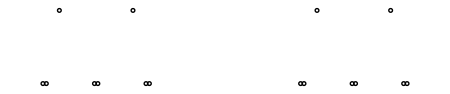

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["config1.dat", Join[Δ,xy0]];
Export["circ1.png", t1];
```

## Circuito Convencional 345kV+ Circuito convencional 500kV

```mathematica
xy0={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
xy0a={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},{0.000,10.736},{0.229,11.132},{-0.229,11.132},{11.000,10.736},{10.771,11.132},{11.229,11.132},{-6.000,22.000},{6.000,22.000}};
```

```mathematica
Δ=Table[xy0[[i]]+{55,0},{i,Length[xy0]}];
```

```mathematica
mostra1={Circle[#,.25]}&/@Join[Δ,xy0a];
```

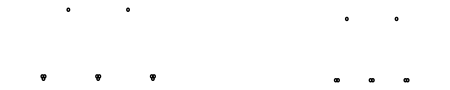

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["config2.dat",Join[Δ,xy0a]];
Export["circ2.png", t1];
```

## Circuito Compacto 500kV + Circuito Convencional 500kV

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
Δ=Table[xy4[[i]]+{65,0},{i,Length[xy4]}];
```

```mathematica
mostra1={Circle[#,.25]}&/@xy5;
```

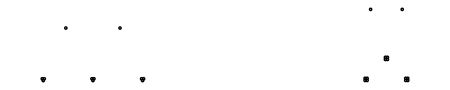

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
Export["config3.dat", xy5 ];
Export["circ3.png", t1];
```

## Circuito 750kV

```mathematica
xa={-15.8,0.0,15.8,52.7,68.5,84.3};
xpr={-14.4,14.4,54.1,82.9};
yca={ 34.76,35.26,34.76,34.76,35.26,34.76};
ycb={13.35,13.85,13.35,13.35,13.85,13.35};
ycc=yca/3+ycb 2/3;
ypra={40.96,40.96,40.96,40.96};
yprb={26.44,26.44,28.56,28.56};
ypr=ypra/3+yprb 2/3;
```

```mathematica
Θx[ns_]:=Table[Cos[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
Θy[ns_]:=Table[Sin[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
xc=Flatten@Join[{Flatten@Table[xa[[i]]+.457 Θx[4],{i,6}],xpr}];
yc=Flatten@Join[{Flatten@Table[ycc[[i]]+.457 Θy[4],{i,6}],ypr}];
```

```mathematica
Dimensions[xc]
```

{28}

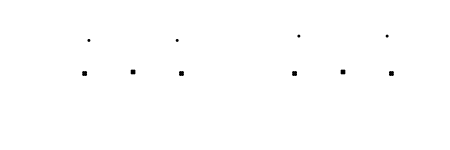

```mathematica
mostra9=({Circle[#1,0.25]}&)/@xy9;
t9=Show[Graphics[mostra9],AspectRatio->Automatic,Axes->False,Frame->Automatic,
PlotRange->{{-30,90},{0,40}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
Export["config4.dat", xy9 ];
Export["circ4.png", t1];
```